### SHO : the Jacobian and ξ

```mathematica
eqs= {η/4(ω v^3+3 u^2 du+v^2 du + u^2 ω v + 2 u v dv) +γ du + (ω0^2  - ω^2) u + γ ω v + 2 ω dv-F Cos[ϕ],η/4(ω u^3+u^2 dv+3 v^2 dv - v^2 ω u + 2 u v du)+(ω0^2-ω^2)v + γ dv - 2 ω du- γ ω u + F Sin[ϕ]} ;
```

```mathematica
sform = Solve[eqs==0, {du ,dv}][[1]];
J[F_, vars_]:={{D[F[[1]], vars[[1]]], D[F[[1]], vars[[2]]]},{D[F[[2]], vars[[1]]], D[F[[2]], vars[[2]]]}}
shoJ = {{D[du /. sform , u], D[du /. sform, v]},{D[dv /. sform , u], D[dv /. sform, v]}}//FullSimplify;
shoJ = J[{du,dv}/.sform, {u,v}] //FullSimplify;
shoJ//MatrixForm

(* collect ξ *)
coeffs=CoefficientList[Collect[{du,dv}/.sform,F], F][[All,2]]
ξ=coeffs /. {Cos[ϕ] -> 1/2, Sin[ϕ] -> -I/2} //FullSimplify
```

((4 (-16 u η (8 γ+3 (u^2+v^2) η) (-1/16 (4 γ+(u^2+3 v^2) η) (ω (4 v γ+u^2 v η+v^3 η-4 u ω)+4 u ω0^2-4 F Cos[ϕ])+1/8 (u v η+4 ω) (-ω (4 u γ-u^3 η+u v^2 η+4 v ω)+4 v ω0^2+4 F Sin[ϕ]))-((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2) (-u^3 v η^2 ω+u v η (8 γ+3 v^2 η) ω+3 u^2 η (-3 ω^2+ω0^2)+(4 γ+v^2 η) (ω^2+ω0^2)-2 F η (u Cos[ϕ]+v Sin[ϕ]))))/(((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2)^2) | -(64 v η (8 γ+3 (u^2+v^2) η) (-1/16 (4 γ+(u^2+3 v^2) η) (ω (4 v γ+u^2 v η+v^3 η-4 u ω)+4 u ω0^2-4 F Cos[ϕ])+1/8 (u v η+4 ω) (-ω (4 u γ-u^3 η+u v^2 η+4 v ω)+4 v ω0^2+4 F Sin[ϕ]))+((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2) (ω (16 γ^2+16 (u^2+3 v^2) γ η+(-u^4+18 u^2 v^2+15 v^4) η^2+8 u v η ω+32 ω^2)+8 (u v η-4 ω) ω0^2-8 F η (3 v Cos[ϕ]+u Sin[ϕ])))/(((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2)^2)
(4 u η (8 γ+3 (u^2+v^2) η) (3 u^5 η^2 ω-4 u^3 η (2 γ+v^2 η) ω+4 u^2 v η (ω^2+ω0^2)+4 v (4 γ+v^2 η) (ω^2+ω0^2)-u ω ((4 γ+v^2 η) (4 γ+3 v^2 η)+32 (ω-ω0) (ω+ω0))+8 F (u v η-4 ω) Cos[ϕ]+4 F (4 γ+(3 u^2+v^2) η) Sin[ϕ])+((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2) (ω (16 γ^2+8 (3 u^2+2 v^2) γ η+3 (-5 u^4+4 u^2 v^2+v^4) η^2-8 u v η ω+32 ω^2)-8 (u v η+4 ω) ω0^2-8 F η (v Cos[ϕ]+3 u Sin[ϕ])))/(((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2)^2) | (-4 v η (8 γ+3 (u^2+v^2) η) (-3 u^5 η^2 ω+4 u^3 η (2 γ+v^2 η) ω-4 u^2 v η (ω^2+ω0^2)-4 v (4 γ+v^2 η) (ω^2+ω0^2)+u ω ((4 γ+v^2 η) (4 γ+3 v^2 η)+32 (ω-ω0) (ω+ω0))-8 F (u v η-4 ω) Cos[ϕ]-4 F (4 γ+(3 u^2+v^2) η) Sin[ϕ])+4 ((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2) (2 u^3 v η^2 ω+u v η (8 γ+3 v^2 η) ω-u^2 η (ω^2+ω0^2)-(4 γ+3 v^2 η) (ω^2+ω0^2)-2 F η (u Cos[ϕ]+v Sin[ϕ])))/(((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2)^2))

{-((γ+(u^2 η)/4+(3 v^2 η)/4) Cos[ϕ]+((u v η)/2+2 ω) Sin[ϕ])/(-γ^2-u^2 γ η-v^2 γ η-(3 u^4 η^2)/16-3/8 u^2 v^2 η^2-(3 v^4 η^2)/16-4 ω^2),-(8 u v η Cos[ϕ]-32 ω Cos[ϕ]+16 γ Sin[ϕ]+12 u^2 η Sin[ϕ]+4 v^2 η Sin[ϕ])/(16 γ^2+16 u^2 γ η+16 v^2 γ η+3 u^4 η^2+6 u^2 v^2 η^2+3 v^4 η^2+64 ω^2)}

{(2 (4 γ+(u+ⅈ v) (u-3 ⅈ v) η-8 ⅈ ω))/((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2),(8 ⅈ γ+2 (u+ⅈ v) (3 ⅈ u+v) η+16 ω)/((4 γ+(u^2+v^2) η) (4 γ+3 (u^2+v^2) η)+64 ω^2)}

```mathematica
{λs, vs} = Eigensystem[(shoJ+I ω PauliMatrix[0])/.η->0]//FullSimplify
```

{{-(ω^2+ω0^2)/(γ+2 ⅈ ω),(2 ⅈ γ ω+3 ω^2-ω0^2)/(γ-2 ⅈ ω)},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
λ1=λs[[1]]; (* the eigenvalue associated with {1, I} *)
δU=ξ/(I Ω-λ1)/.η->0//FullSimplify;
a =Norm[δU] √2//FullSimplify//ComplexExpand
δx =(Re[δU[[1]]] +Im[δU[[2]]]) Cos[Ω t]-(Im[δU[[1]]] -Re[δU[[2]]])Sin[Ω t]//ComplexExpand//FullSimplify
```

1/(√(γ^2 Ω^2+(ω^2-2 ω Ω+ω0^2)^2))

((ω^2-2 ω Ω+ω0^2) Cos[t Ω]+γ Ω Sin[t Ω])/(ω^4-4 ω^3 Ω+γ^2 Ω^2+4 ω^2 Ω^2+2 ω (ω-2 Ω) ω0^2+ω0^4)

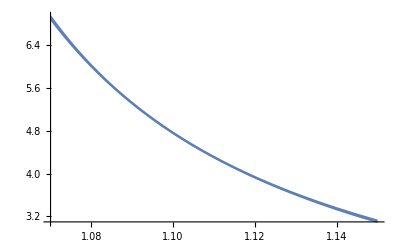

```mathematica
Lor= 1/(√((ω0^2-Ω^2)^2+(γ Ω)^2));
Plot[{a, Lor}/.{ω0->1, ω->1.1, Ω->o, γ->0.01},{o,1.07,1.15}]
```

```mathematica
Solve[D[a, Ω]==0, Ω]
```

{{Ω→(2 (ω^3+ω ω0^2))/(γ^2+4 ω^2)}}

## beyond the Jacobian

```mathematica
eqsFull= {ddu+γ du + (ω0^2  - ω^2) u + γ ω v + 2 ω dv-F Cos[ϕ],ddv+(ω0^2-ω^2)v + γ dv - 2 ω du- γ ω u + F Sin[ϕ]} ;
J2 = J[ eqsFull , {ddu,ddv}]
J1 = J[ eqsFull, {du,dv}]
J0 = J[ eqsFull , {u,v}]

M = -Ω^2 J2 + (2 J2 ω IdentityMatrix[2] + I J1) Ω - J2 ω^2 IdentityMatrix[2] - I J1 ω + J0;
```

{{1,0},{0,1}}

{{γ,2 ω},{-2 ω,γ}}

{{-ω^2+ω0^2,γ ω},{-γ ω,-ω^2+ω0^2}}

```mathematica
{λs, vs} = Eigensystem[M]//FullSimplify
```

{{ⅈ γ Ω-Ω^2+ω0^2,(2 ω-Ω) (-ⅈ γ-2 ω+Ω)+ω0^2},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
ξ = {1/2, I/2}
λ1=λs[[1]];
δU=ξ/λ1/.η->0//FullSimplify;
a =Norm[δU] √2//FullSimplify//ComplexExpand
δx =(Re[δU[[1]]] +Im[δU[[2]]]) Cos[Ω t]-(Im[δU[[1]]] -Re[δU[[2]]])Sin[Ω t]//ComplexExpand//FullSimplify
```

{1/2,ⅈ/2}

√(1/(γ^2 Ω^2+(Ω^2-ω0^2)^2)) Cos[1/2 Arg[1/((-ⅈ γ Ω+Ω^2-ω0^2) (ⅈ Conjugate[γ] Conjugate[Ω]+Conjugate[Ω]^2-Conjugate[ω0]^2))]]+ⅈ √(1/(γ^2 Ω^2+(Ω^2-ω0^2)^2)) Sin[1/2 Arg[1/((-ⅈ γ Ω+Ω^2-ω0^2) (ⅈ Conjugate[γ] Conjugate[Ω]+Conjugate[Ω]^2-Conjugate[ω0]^2))]]

((-Ω^2+ω0^2) Cos[t Ω]+γ Ω Sin[t Ω])/(γ^2 Ω^2+(Ω^2-ω0^2)^2)

```mathematica
Inverse[M].ξ;
Norm[%] √2//FullSimplify
```

2/Abs[2 γ Ω+2 ⅈ (Ω-ω0) (Ω+ω0)]